28.3465

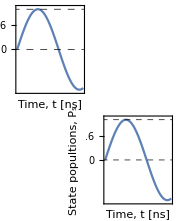

```mathematica
cm=72/2.54

imageSize=4.8cm;

iPwB=1;
iPwS=0.025;

iPhB=1.1;
iPhS=0.025;

imagePaddingBroad={{iPwB cm,iPwS cm},{iPhB cm,iPhS cm}};
imagePaddingSmall={{iPwS cm,iPwS cm},{iPhS cm,iPhS cm}};


plotMarkersG=Graphics[{glvlColor,Disk[]},ImageSize->3.2];


fontSize=8;

plotOPtions={
		PlotRange->{{0,5},{-1.05,1.05}} ,
			ImageSize->imageSize+Total[imagePaddingBroad⟦1⟧],
			Frame-> True,
		ImagePadding->imagePaddingBroad,
		  LabelStyle-> Directive[FontSize-> fontSize,FontFamily->"Arial"],
			FrameStyle->Directive[Black,AbsoluteThickness[0.5]],
			GridLines->{None, {0,1}},
	           GridLinesStyle->Directive[Black, AbsoluteThickness[0.5],Dashing[0.03]],
			FrameLabel->{{"State popultions, "<>ToString[Subscript["P",Style["s",FontFamily->6]],TraditionalForm],None},{"Time, t [ns]",None}},
		AspectRatio->1/ GoldenRatio,
Axes-> False,
FrameTicks-> {{{0,{0.2,".2"},{0.4,".4"},{0.6,".6"},{0.8,".8"},1},{0,{0.2,".2"},{0.4,".4"},{0.6,".6"},{0.8,".8"},1}},{{-30,0,30,60,90,120,150},None}}

};

plot1=Plot[Sin[x],{x,0,5},Evaluate[plotOPtions]];
plot2=Plot[Sin[x],{x,0,5},	ImageSize->imageSize+Total[imagePaddingSmall⟦1⟧],ImagePadding->imagePaddingSmall,Evaluate[plotOPtions]];
Magnify[plot1,3];
Magnify[plot2,3];

spacingw=0.15 cm;
spacingh=0.15 cm;

extra=0.1cm;

w=  imageSize+Total[imagePaddingBroad⟦1⟧];
h=2*w/GoldenRatio(*2.5*  imageSize/GoldenRatio+Total[imagePaddingBroad⟦2⟧]*);
combined=Graphics[{
Inset[plot1, {(imageSize+Total[imagePaddingBroad⟦1⟧])/2,4cm}],
Inset[plot2, {imagePaddingBroad⟦1,1⟧-imagePaddingSmall⟦1,1⟧+(imageSize+Total[imagePaddingSmall⟦1⟧])/2,2cm}]}
,PlotRange->{{0,w+2*spacingw+extra},{0,h+2*spacingh+extra}},ImageSize->{w+2*spacingw+extra,h+2*spacingh+3*extra}

];

Magnify[combined,3]
```

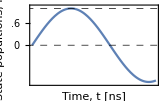

-Graphics-

-Graphics-